# Jakub Zbrzezny Numer indeksu: 286689 Numer na liście obecności: 6

Rozważamy uproszczony problem trzech ciał, jak na rysunku poniżej (na prawym rysunku znajduje się powiększenie fragmentu rysunku z lewej).

-Graphics-
Rysunek jest wzięty z pliku z zadaniami na zaliczenie z laboratorium #5.

Dane są następujące parametry:
a) M_1 i M_2 - masy dwóch “dużych” ciał (masa trzeciego, tzn. M_3 jest pomijalnie mała),
b) R_(i,0) i V_(i,0) - położenie i prędkość początkowa i-tego ciała (i = 1,2,3).

Zakładamy, że środek masy tego układu nie porusza się, ruch odbywa się w jednej płaszczyźnie, masy są unormowane, tzn. M_1 + M_2 = 1, a G = 1, gdzie G to stała grawitacji.
Szukamy trajektorii R_1, R_2 i R_3 wszystkich trzech ciał.

-Graphics-
Rysunek jest zrobiony w programie Paint.

Z prawa powszechnego ciążenia mamy:
- F_12 = -F_21 = G (M_1 M_2)/(R_1 - R_2)^2 (R_2 - R_1)/(|R_1 - R_2|),
- F_13 = -F_31 = G (M_1 M_3)/(R_1 - R_3)^2  (R_3 - R_1)/(|R_1 - R_3|),
- F_23 = -F_32 = G (M_2 M_3)/(R_2 - R_3)^2  (R_3 - R_2)/(|R_2 - R_3|).

Ponadto, z II zasady dynamiki Newtona, zastosowanej do poruszającego się ciała o masie M_1 i ciała o masie M_2 :
- M_1 R_1’’(t) = F_12,
- M_2 R_2’’(t) = F_21 = - F_12.

Zatem z dwóch powyższych równań mamy: M_1 R_1’’(t) + M_2 R_2’’(t) = 0.
Położeniem środka masy jest: R = (M_1 R_1 + M_2 R_2)/(M_1 + M_2).

Stąd otrzymujemy, że (M_1 + M_2) R’’ = 0, a zatem R’’ = const, czyli R’(t) = c, gdzie c jest stałą. 
Czyli środek masy porusza się ze stałą prędkością, a więc bez utraty ogólności rozważań możemy przyjąć, że R(t) = (0,0).
Zatem (M_1 R_1 + M_2 R_2)/(M_1 + M_2) = 0 (#).

Weźmy r = R_1 - R_2.
Z (#) mamy: R_1 = M_2/(M_1 + M_2) r  oraz R_2 = - M_1/(M_1 + M_2) r.

Zauważmy, że r’’ = - G(M_1 + M_2) r/(|r|^3).
Stąd r_x’’ = - G(M_1 + M_2)  r_x/(((r_x)^2+(r_y)^2)^(3/2)) oraz r_y’’ =  - G(M_1 + M_2) r_y/(((r_x)^2+(r_y)^2)^(3/2)).

Ponadto,z II zasady dynamiki, dla ciała o masie M_3:
	M_3 R_3’’(t) = G M_1 M_3 (R_1 - R_3)/(|R_1 - R_3|^3) + G M_2 M_3  (R_2 - R_3)/(|R_2 - R_3|^3) (*).

Wiemy, że:
a) M_1 = 0,2,
b) R_(1,0) = (0,2), V_(1,0) = (0,5, 0,5),
c) R_(3,0) = (-1,0), V_(3,0) = (0, -1).

```mathematica
M1 = 0.2;
```

```mathematica
M2 =1 -M1;
```

```mathematica
G = 1;
```

```mathematica
R10 = {0,2};
```

```mathematica
R1p0= {0.5, 0.5};
```

```mathematica
R30 = {-1,0};
```

```mathematica
R3p0={0,-1};
```

```mathematica
eq1 = rx''[t] == - G (M1 + M2) rx[t]/(((rx[t])^2 + (ry[t])^2)^(3/2));
eq2 = ry''[t] == -G (M1 + M2) ry[t]/(((rx[t])^2 + (ry[t])^2)^(3/2));
sol1 = NDSolve[{eq1,eq2,rx[0]== R10[[1]]/M2, ry[0] == R10[[2]]/M2, rx'[0] == R1p0[[1]]/M2, ry'[0] == R1p0[[2]]/M2}, {rx,ry}, {t,0,5000}]
```

{{rx→InterpolatingFunction[…],ry→InterpolatingFunction[…]}}

```mathematica
r[t_] = {rx[t], ry[t]}/.sol1[[1]];
```

```mathematica
R1[t_] = M2/(M1+M2) r[t];
```

```mathematica
R2[t_] = -M1/(M1+M2) r[t];
```

Teraz narysujemy trajektorie R_1(t), R_2(t).

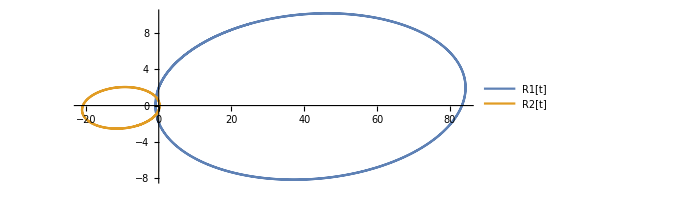

```mathematica
ParametricPlot[{R1[t],R2[t]},{t,0,5000},PlotLegends->{"R1[t]","R2[t]"}]
```

```mathematica
R1x[t_]=R1[t][[1]];
R1y[t_]=R1[t][[2]];
R2x[t_]=R2[t][[1]];
R2y[t_]=R2[t][[2]];
```

Po podzieleniu stronami równania (*) przez M_3 rozwiązujemy następujące równania:

```mathematica
sol2=NDSolve[{R3x''[t]==G M1   (R1x[t] -R3x[t])/(((R1x[t] - R3x[t])^2 +(R1y[t] - R3y[t])^2)^(3/2)) + G M2   (R2x[t] - R3x[t])/(((R2x[t] - R3x[t])^2 +( R2y[t] - R3y[t])^2)^(3/2)),
R3y''[t]==G M1   (R1y[t] -R3y[t])/(((R1x[t] - R3x[t])^2 +(R1y[t] - R3y[t])^2)^(3/2)) + G M2   (R2y[t] - R3y[t])/(((R2x[t] - R3x[t])^2 +(R2y[t] - R3y[t])^2)^(3/2)),  R3x[0]==R30[[1]], R3y[0] == R30[[2]], R3x'[0]==R3p0[[1]],R3y'[0]==R3p0[[2]]},{R3x,R3y},{t,0,5000},MaxSteps->10^9]
```

{{R3x→InterpolatingFunction[{{0., 5000.}}, <>],R3y→InterpolatingFunction[{{0., 5000.}}, <>]}}

Narysujemy trajektorię

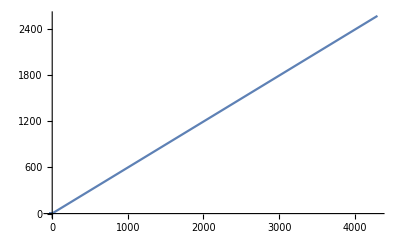

```mathematica
ParametricPlot[Evaluate[{R3x[t],R3y[t]}/.sol2],{t,0,5000}]
```

```mathematica
(*pierwsze równanie równanie - dwa ciała*)
Rx=rx/.sol1[[1]];
Ry = ry/.sol1[[1]]; 
(*drugie równanie - trzy ciała*)
R3x = R3x/.sol2[[1]];
R3y = R3y/.sol2[[1]];
TR1 = {#, M2/(M1 + M2) Rx[#], M2/(M1 + M2) Ry[#]}&/@First[Rx@"Coordinates"];
TR2={#,-M1/(M1 + M2) Rx[#], -M1/(M1+M2) Ry[#]}&/@First[Rx@"Coordinates"];
TR3={#,R3x[#],R3y[#]}&/@First[R3x@"Coordinates"];
```

Uzyskane wyniki eksportujemy do pliku trajektorie.mat, żeby później skorzystać z tego na kolejnych zajęciach.

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"trajektorie.mat"}],{"R1"->TR1,"R2"->TR2,"R3"->TR3},"LabeledData"]
```

C:\Users\Użytkownik\Documents\trajektorie.mat

Tworzymy animację ruchu 3 ciał w układzie.

```mathematica
Manipulate[
Show[
ParametricPlot[{R1[s],R2[s]},{s,0,t}],
ParametricPlot[Evaluate[{R3x[s],R3y[s]}/.sol2],{s,0,t}],
PlotRange->{{-40,85},{-75,85}}],
{t,0.01,5000}]
```